```mathematica
(*Project Euler*)
```

```mathematica
(*501: Eight Divisors*)
v=0;SetSharedVariable[v];ParallelDo[If[Length@Divisors@i==8,v+=1],{i,0,160}];v
```

22

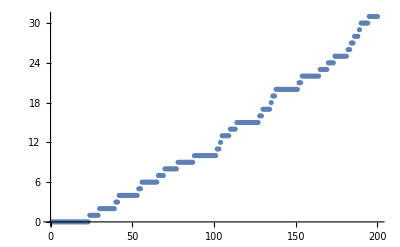

```mathematica
ListPlot[Length@Select[Range@#,Length@Divisors@#==8&]&/@Range@200]
```

```mathematica
Prime@Range@100
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}

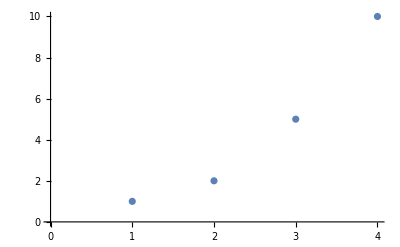

```mathematica
ListPlot@Divisors@10
```